```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v2/datav3

```mathematica
dataall=Table[Import["./Shi_700-870_band=30_nodes=51/Shi_mu="<>ToString[i]<>"_m0=700.0-flag_4-51x120_VC=true.csv"],{i,700,870,5}];
```

```mathematica
n=Length[Table[i,{i,700,870,5}]]
```

35

```mathematica
dataall[[1]]
```

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*120+i]][[5]],{i,2,121}],{j,0,50}],{n1,1,35}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[(i-1)*5+700]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,35}],{j,1,51}];
```

```mathematica
T=Table[i,{i,1,120}];
```

```mathematica
Length[pdata[[1]]]
```

51

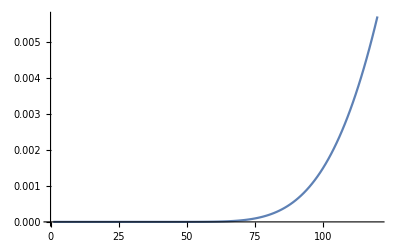

```mathematica
ListLinePlot[pdata[[1]][[10]]*197.33^3/T^4,PlotRange->All]
```